# Transient

```mathematica
(*************************************** Analytical expressions ***************************************)

(*
Abbreviations:
k = k_F^- and kf = k_F^+
A = A_F and B = D_F
*)

k=A*B; kf=B-k;
Id=({{1, 0}, {0, 1}}); km=({{-kf, k}, {kf, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, R}}); Rem=({{r, R}});(*Useful matrices*)

dlsv0=Inverse[(s*Id-km)].Iv; (*Subscript[ΔL^(->), s]^(0): Eq. S12 with x=0 *)
dlsv1=Inverse[(s*Id-km)].Ret.dlsv0; (*Subscript[ΔL^(->), s]^(1): Eq. S12 with x=1 *)

dls=1/s*Rem.dlsv0; (* <Subscript[ΔL, s]^1>: Eq. S8 with n=1 *)
dl2s=1/s*Rem.dlsv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S8 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S13 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t];(* <Subscript[ΔL, t]^2>: Eq. S13 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)

Simplify[dlt]
Simplify[vt]

Quit[];
```

(r-A r+(-1+A) ⅇ^(-B t) (r-R)-R+A R+B (A (r-R)+R) t)/B

((-1+A) ⅇ^(-2 B t) (-1+ⅇ^(B t)) (-1+A-ⅇ^(B t)+5 A ⅇ^(B t)) (r-R)^2)/B^2+(A (r-R)+R) t-1/B(-1+A) ⅇ^(-B t) (r-R) (-1+2 (-1+2 A) r t+2 R t-4 A R t+ⅇ^(B t) (1+2 A (r-R) t))

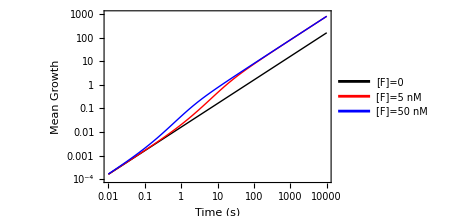
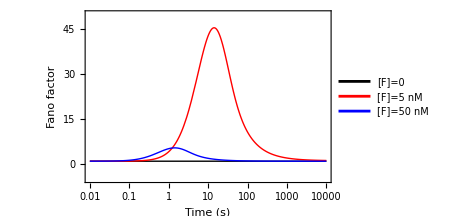
-Graphics- | -Graphics-

```mathematica
(*************************************** Plot ***************************************)
(*Off[General::munfl];*)

B=k+kf; A=k/B;

dlt=(r-A r+(-1+A) ⅇ^(-B t) (r-R)-R+A R+B (A (r-R)+R) t)/B;
vt=((-1+A) ⅇ^(-2 B t) (-1+ⅇ^(B t)) (-1+A-ⅇ^(B t)+5 A ⅇ^(B t)) (r-R)^2)/B^2+(A (r-R)+R) t-1/B(-1+A) ⅇ^(-B t) (r-R) (-1+2 (-1+2 A) r t+2 R t-4 A R t+ⅇ^(B t) (1+2 A (r-R) t));
ft=vt/dlt;

kf=kfp*F;

r=6;
R=30;                  
k=8.1*10^-5;            
kfp=29.1*10^-3;        
scalingFactor=27/10000; 

(*Convert machine-precision k and kcp to high-precision*)
highPrecisionRules={k->SetPrecision[8.1*10^-5,30],kfp->SetPrecision[29.1*10^-3,30]};

(*Numerically evaluate functions*)dlt0=N[dlt/. {F->0}/. highPrecisionRules,30];
dlt5=N[dlt/. {F->5}/. highPrecisionRules,30];
dlt50=N[dlt/. {F->50}/. highPrecisionRules,30];

ft0=N[ft/. {F->0}/. highPrecisionRules,30];
ft5=N[ft/. {F->5}/. highPrecisionRules,30];
ft50=N[ft/. {F->50}/. highPrecisionRules,30];

ti=1/100; tf=10^4;
p1=Quiet[LogLogPlot[{dlt0*scalingFactor,dlt5*scalingFactor,dlt50*scalingFactor},{t,ti,tf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Mean Growth"},ImageSize->350,PlotLegends->{"[F]=0","[F]=5 nM", "[F]=50 nM"},PlotRange->{{10^-2,10^4},{10^-4,10^3}}],{LogLogPlot::precw,LogLinearPlot::precw}];

p2=Quiet[LogLinearPlot[{ft0,ft5,ft50},{t,ti,tf},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Fano factor"},ImageSize->350,PlotLegends->{"[F]=0","[F]=5 nM", "[F]=50 nM"},PlotRange->{{10^-2,10^4},{-5,50}}],{LogLogPlot::precw,LogLinearPlot::precw}];

Grid[{{p1,p2}}]

Quit[];
```

```mathematica
(*************************************** Data export ***************************************)
Off[General::munfl];

Id=({{1, 0}, {0, 1}}); km=({{-kf, k}, {kf, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, R}}); Rem=({{r, R}});(*Useful matrices*)

dlsv0=Inverse[(s*Id-km)].Iv; (*Subscript[ΔL^(->), s]^(0): Eq. S12 with x=0 *)
dlsv1=Inverse[(s*Id-km)].Ret.dlsv0; (*Subscript[ΔL^(->), s]^(1): Eq. S12 with x=1 *)

dls=1/s*Rem.dlsv0; (* <Subscript[ΔL, s]^1>: Eq. S8 with n=1 *)
dl2s=1/s*Rem.dlsv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S8 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S13 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t];(* <Subscript[ΔL, t]^2>: Eq. S13 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2; (* Variance *)
ft=vt/dlt;

kf=kfp*F;

r=6;
R=30;                  
k=8.1*10^-5;            
kfp=29.1*10^-3;        
scalingFactor=27/10000; 

(*Data Format*)
toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

ti=0.01; 
tf1=0.1; tf2=1; tf3=10; tf4=100; tf5=1000; tf6=10000;
dt1=0.0009; dt2=0.009; dt3=0.09; dt4=0.9; dt5=9; dt6=90;

Clear[F];
F=0;
tb11=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb12=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb13=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb14=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb15=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb16=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\t-dl-f-F0.dat",tbp1,"FieldSeparators"->"    "];


Clear[F];
F=5;
tb21=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb22=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb23=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb24=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb25=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb26=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb2=Join[tb21,tb22,tb23,tb24,tb25,tb26];
tbp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb2];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\t-dl-f-F5.dat",tbp2,"FieldSeparators"->"    "];


Clear[F];
F=50;
tb31=Table[{t,dlt*0.0027,ft},{t,ti,tf1,dt1}];
tb32=Table[{t,dlt*0.0027,ft},{t,tf1+dt2,tf2,dt2}];
tb33=Table[{t,dlt*0.0027,ft},{t,tf2+dt3,tf3,dt3}];
tb34=Table[{t,dlt*0.0027,ft},{t,tf3+dt4,tf4,dt4}];
tb35=Table[{t,dlt*0.0027,ft},{t,tf4+dt5,tf5,dt5}];
tb36=Table[{t,dlt*0.0027,ft},{t,tf5+dt6,tf6,dt6}];
tb3=Join[tb31,tb32,tb33,tb34,tb35,tb36];
tbp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb3];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\t-dl-f-F50.dat",tbp3,"FieldSeparators"->"    "];


Quit[];
```

# Long-time Limit

```mathematica
(*************************************** Analytical expressions ***************************************)

(*
Abbreviations:
k = k_F^- and kf = k_F^+
A = A_F and B = D_F
*)

k=A*B; kf=B-k;
Id=({{1, 0}, {0, 1}}); km=({{-kf, k}, {kf, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, R}}); Rem=({{r, R}});(*Useful matrices*)

dltv01=({{p1}, {p2}}); Y=({{1, 1}});
e1=km.dltv01; (*Eq (S14)*)
e2=Y.dltv01; (*Eq (S15)*)
eq1=e1[[1,1]]; eq2=e1[[2,1]]; eq3=e2[[1,1]];
sol=Solve[{eq1==0,eq3==1},{p1,p2}];
p11=p1/.sol[[1,1]];
p12=p2/.sol[[1,2]];

dltv0=({{p11}, {p12}});

dlsv1=1/s*Inverse[(s*Id-km)].Ret.dltv0; (*Subscript[ΔL^(->), s]^(1): Eq. S17 with x=1 *)

dls=1/s^2*Rem.dltv0; (* <Subscript[ΔL, s]^1>: Eq. S16 with n=1 *)
dl2s=1/s^2*Rem.dltv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S16 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S18 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t]; (* <Subscript[ΔL, t]^2>: Eq. S18 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2 ;(* Variance *)

FullSimplify[dlt]
FullSimplify[vt]

Quit[];
```

(A (r-R)+R) t

1/B^2 ⅇ^(-B t) (B^2 ⅇ^(B t) R t-2 A^2 (r-R)^2 (1+ⅇ^(B t) (-1+B t))+A (r-R) (2 r-2 R+ⅇ^(B t) (-2 r+2 R+B (B+2 r-2 R) t)))

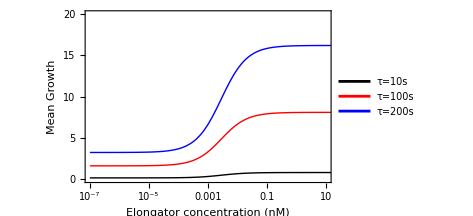
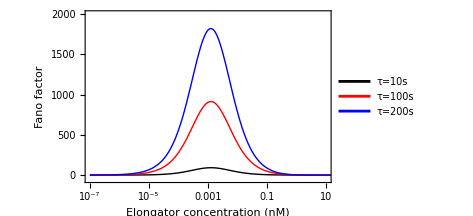
-Graphics- | -Graphics-

```mathematica
(*************************************** Plot ***************************************)
(*Off[General::munfl];*)
B=k+kf; A=k/B;

dlt=(A (r-R)+R) t;
vt=1/B^2 ⅇ^(-B t) (B^2 ⅇ^(B t) R t-2 A^2 (r-R)^2 (1+ⅇ^(B t) (-1+B t))+A (r-R) (2 r-2 R+ⅇ^(B t) (-2 r+2 R+B (B+2 r-2 R) t)));
ft=vt/dlt;

kf=kfp*F;

r=6;
R=30;                  
k=8.1*10^-5;            
kfp=29.1*10^-3;        
scalingFactor=27/10000; 

(*Convert machine-precision k and kcp to high-precision*)
highPrecisionRules={k->SetPrecision[8.1*10^-5,30],kfp->SetPrecision[29.1*10^-3,30]};

(*Apply high precision to dlt0,dlt5,dlt50*)
dlt10=dlt/. {t->10}/. highPrecisionRules;
dlt100=dlt/. {t->100}/. highPrecisionRules;
dlt200=dlt/. {t->200}/. highPrecisionRules;

ft10=ft/. {t->10}/. highPrecisionRules;
ft100=ft/. {t->100}/. highPrecisionRules;
ft200=ft/. {t->200}/. highPrecisionRules;

Fi=10^-7; Ff=10^7;
p1=Quiet[LogLinearPlot[{dlt10*scalingFactor,dlt100*scalingFactor,dlt200*scalingFactor},{F,Fi,Ff},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Elongator concentration (nM)","Mean Growth"},ImageSize->350,PlotLegends->{"τ=10s","τ=100s", "τ=200s"},PlotRange->{{10^-7,10},{0,20}}],{LogLogPlot::precw,LogLinearPlot::precw}];

p2=Quiet[LogLinearPlot[{ft10,ft100,ft200},{F,Fi,Ff},WorkingPrecision->30,Frame->True,GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Elongator concentration (nM)","Fano factor"},ImageSize->350,PlotLegends->{"τ=10s","τ=100s", "τ=200s"},PlotRange->{{10^-7,10},{-50,2000}}],{LogLogPlot::precw,LogLinearPlot::precw}];

Grid[{{p1,p2}}]

Quit[];
```

```mathematica
(*************************************** Data export ***************************************)
Off[General::munfl];

Id=({{1, 0}, {0, 1}}); km=({{-kf, k}, {kf, -k}}); Iv=({{1}, {0}}); Ret=({{r, 0}, {0, R}}); Rem=({{r, R}});(*Useful matrices*)

dltv01=({{p1}, {p2}}); Y=({{1, 1}});
e1=km.dltv01; (*Eq (S14)*)
e2=Y.dltv01; (*Eq (S15)*)
eq1=e1[[1,1]]; eq2=e1[[2,1]]; eq3=e2[[1,1]];
sol=Solve[{eq1==0,eq3==1},{p1,p2}];
p11=p1/.sol[[1,1]];
p12=p2/.sol[[1,2]];

dltv0=({{p11}, {p12}});

dlsv1=1/s*Inverse[(s*Id-km)].Ret.dltv0; (*Subscript[ΔL^(->), s]^(1): Eq. S17 with x=1 *)

dls=1/s^2*Rem.dltv0; (* <Subscript[ΔL, s]^1>: Eq. S16 with n=1 *)
dl2s=1/s^2*Rem.dltv0+2/s*Rem.dlsv1; (* <Subscript[ΔL, s]^2>: Eq. S16 with n=2 *)

dltm=InverseLaplaceTransform[dls,s,t]; (* <Subscript[ΔL, t]>: Eq. S18 with n=1 *)
dl2tm=InverseLaplaceTransform[dl2s,s,t]; (* <Subscript[ΔL, t]^2>: Eq. S18 with n=2 *)

dlt=dltm[[1,1]]; (* <Subscript[ΔL, t]> *)
dl2t=dl2tm[[1,1]]; (* <Subscript[ΔL, t]^2> *)
vt=dl2t-dlt^2 ;(* Variance *)
ft=vt/dlt;

kf=kfp*F;

r=6;
R=30;                  
k=8.1*10^-5;            
kfp=29.1*10^-3;        
scalingFactor=27/10000; 

(*Convert machine-precision k and kcp to high-precision*)
highPrecisionRules={k->SetPrecision[8.1*10^-5,30],kfp->SetPrecision[29.1*10^-3,30]};



toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

Fi=10^-9;Ff1=10^-8;  Ff2=10^-7; Ff3=10^-6; Ff4=10^-5; Ff5=10^-4; Ff6=10^-3; Ff7=10^-2; Ff8=10^-1; Ff9=10^0; Ff10=10^1; Ff11=10^2; Ff12=10^3; Ff13=10^4; Ff14=10^5; Ff15=10^6;
df1=0.9*10^-10; df2=0.9*10^-9; df3=0.9*10^-8; df4=0.9*10^-7; df5=0.9*10^-6; df6=0.9*10^-5; df7=0.9*10^-4; df8=0.9*10^-3; df9=0.9*10^-2; df10=0.9*10^-1; df11=0.9*10^0; df12=0.9*10^1; df13=0.9*10^2; df14=0.9*10^3; df15=0.9*10^4;

Clear[t];
t=10;
tb11=Table[{F,dlt*0.0027,ft},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt*0.0027,ft},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt*0.0027,ft},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt*0.0027,ft},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt*0.0027,ft},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt*0.0027,ft},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt*0.0027,ft},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt*0.0027,ft},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt*0.0027,ft},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt*0.0027,ft},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt*0.0027,ft},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt*0.0027,ft},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt*0.0027,ft},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt*0.0027,ft},{F,Ff13+df14,Ff14,df14}];
tb115=Table[{F,dlt*0.0027,ft},{F,Ff14+df15,Ff15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\F-dl-f-tau10.dat",tbp1,"FieldSeparators"->"    "];

Clear[t];
t=100;
tb11=Table[{F,dlt*0.0027,ft},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt*0.0027,ft},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt*0.0027,ft},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt*0.0027,ft},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt*0.0027,ft},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt*0.0027,ft},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt*0.0027,ft},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt*0.0027,ft},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt*0.0027,ft},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt*0.0027,ft},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt*0.0027,ft},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt*0.0027,ft},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt*0.0027,ft},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt*0.0027,ft},{F,Ff13+df14,Ff14,df14}];
tb115=Table[{F,dlt*0.0027,ft},{F,Ff14+df15,Ff15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\F-dl-f-tau100.dat",tbp1,"FieldSeparators"->"    "];

Clear[t];
t=200;
tb11=Table[{F,dlt*0.0027,ft},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt*0.0027,ft},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt*0.0027,ft},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt*0.0027,ft},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt*0.0027,ft},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt*0.0027,ft},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt*0.0027,ft},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt*0.0027,ft},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt*0.0027,ft},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt*0.0027,ft},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt*0.0027,ft},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt*0.0027,ft},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt*0.0027,ft},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt*0.0027,ft},{F,Ff13+df14,Ff14,df14}];
tb115=Table[{F,dlt*0.0027,ft},{F,Ff14+df15,Ff15,df15}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114,tb115];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Two-state-F-model\\GitHub\\F-dl-f-tau200.dat",tbp1,"FieldSeparators"->"    "];

Quit[];
```